## Multiplication

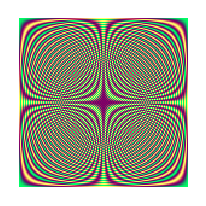
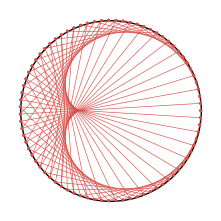
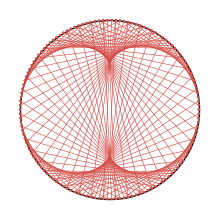
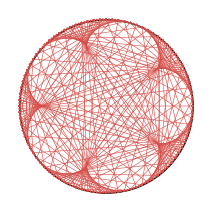
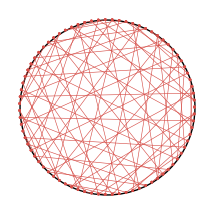
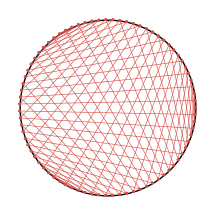

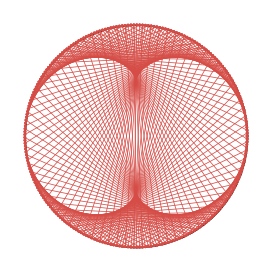
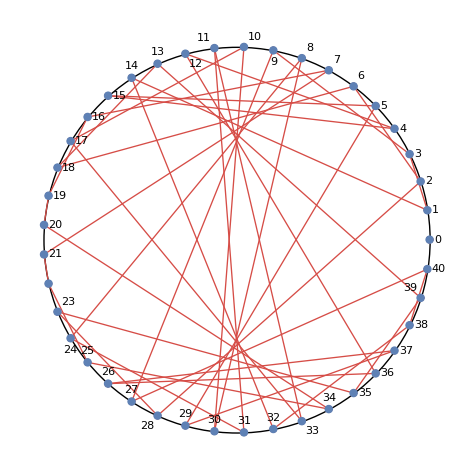

```mathematica
faces={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
Grid[Partition[faces,3]]
```

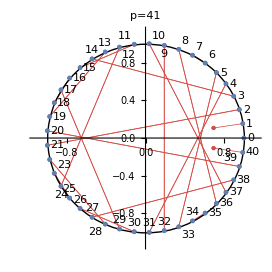
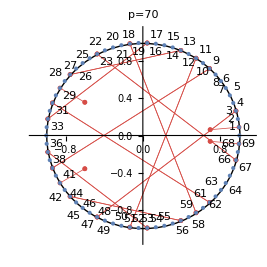
```mathematica
-Graphics--Graphics-
-Graphics--Graphics-
```

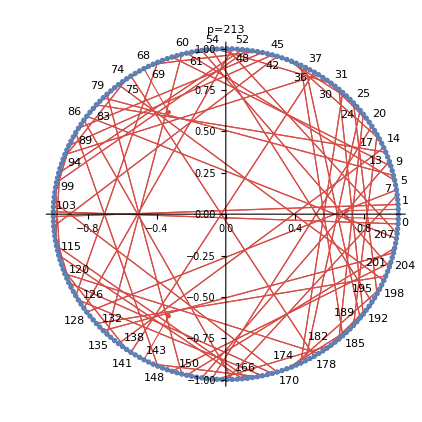
```mathematica
-Graphics--Graphics-
```

## Points on Circle

```mathematica
Graphics[Circle[]]
```

```mathematica
p=19;
circle = Graphics[Circle[{0,0},1]];
points = ListPlot[Table[{Cos[ϕ],Sin[ϕ]}, {ϕ, 0, 2π,2π/p }],AspectRatio->1];
Show[ points, circle]
```

```mathematica
p=19;
circle = Graphics[Circle[]];
points = ListPlot[
Table[{Cos[ϕ], Sin[ϕ]}, {ϕ, 0, 2π,2π/p }],
AspectRatio->1,PlotRange->1.2{{-1,1},{-1,1}} 
];
Manipulate[
line = ParametricPlot[(1.01 + ϕ 0.02/ (2 π))*{Cos[ϕ], Sin[ϕ]}, {ϕ, 0, 2 π x/p +0.01}];
Show[ points, circle, line],
{{x,10},-100,100,1}
]
```

```mathematica
Manipulate[
points = ListPlot[
Table[{Cos[2 π  n / p], Sin[2 π  n/p]}, {n,0,x}],
AspectRatio->1,PlotRange->1.2{{-1,1},{-1,1}} 
];
Show[ points, circle],
{{x,10},-30,30,1}
]
```

```mathematica
Manipulate[
points = ListPlot[
Table[Labeled[(1+ n * 0.00000001){Cos[2 π  n / p], Sin[2 π  n/p]}, n], {n,0,x}],
AspectRatio->1,PlotRange->1.2{{-1,1},{-1,1}} 
];
Show[ points, circle],
{{x,10},-30,30,1}
]
```

## Introduction to Modulus

```mathematica
?? Mod
```

```mathematica
Mod[14 ,5]
```

```mathematica
Mod[17 ,5]
```

```mathematica
Mod[12 ,5]
```

```mathematica
Mod[13 ,5]
```

```mathematica
Mod[17, 5]
```

```mathematica
17*13
```

```mathematica
Mod[17 * 13, 5]
```

```mathematica
Mod[2 * 3, 5]
```

```mathematica
Mod[9212123,100]
```

```mathematica
Mod[9212123,1000]
```

```mathematica
{
102012 * 3332103,
Mod[102012 * 3332103, 1000], 
12 * 103,
Mod[12 * 103, 1000]
}
```

```mathematica
p=1000;
```

```mathematica
a=102012; 
b= 3332103; 
as=Mod[a,p] 
bs=Mod[b,p]
```

```mathematica
{
Mod[a * b, p], 
Mod[as * bs, p]
}
```

```mathematica
Mod[a * b, p] == Mod[  Mod[a,p] * Mod[b,p], p ]
```

```mathematica
Clear[a,b];p=19;
Reduce[Mod[a * b, p] == Mod[  Mod[a,p] * Mod[b,p], p], {a,b}, Integers]
```

```mathematica
Expand[(k1 + 5 m1) * (k2 + 5 m2)]
```

```mathematica
Reduce[Mod[(k1 + 5 m1) * (k2 + 5 m2),5]==Mod[k1 * k2, 5],{k1,k2,m1,m2},Integers]
```

```mathematica
Manipulate[
Grid[Table[
Mod[i+j,p],
{i,0,  p-1},
{j,0,  p-1}
], 
Frame->All
],
{{p, 19}, 1,100, 1}
]
```

```mathematica
Manipulate[
Grid[Table[Mod[i*j,p],{i,0,  p-1}, {j,0,  p-1}], Frame->All],
{{p, 19}, 1,100, 1}
]
```

```mathematica
a (b + c) = a b + a c
```

```mathematica
Manipulate[
ArrayPlot[Table[
Mod[i+j,p],
{i,0,  p-1},
{j,0,  p-1}
]
],
{{p, 5}, 1,500, 1}
]
```

```mathematica
Manipulate[
ArrayPlot[Table[
Mod[i+j,p],
{i,0,  p-1},
{j,0,  p-1}
],
ColorFunction->(RGBColor[Sin[Pi #]^2,Cos[2 Pi #]^2,0.4]&)
],
{{p, 23}, 1,500, 1}
]
```

```mathematica
cf=(RGBColor[Sin[Pi #]^2,Cos[2Pi #]^2,0.4]&);
```

```mathematica
Manipulate[
ArrayPlot[Table[
Mod[i*j,p],
{i,1,  p-1},
{j,1,  p-1}
],ColorFunction->cf
],
{{p, 23}, 1,500, 1}
]
```

```mathematica
Manipulate[
Grid[Table[
Mod[i^j,p],
{j,1,  p-1 },
{i,1,  p-1}
]
],
{{p,23}, 1,100, 1}
]
```

```mathematica
Manipulate[
ArrayPlot[Table[
Mod[a i^j+b ,p],
{j,2,  p-2},
{i,2,  p-2}
],
ColorFunction->cf
],
{{p,67}, 1,100, 1},
{{a,1},1,p-1,1},
{{b,0},0,p-1,1}
]
```

```mathematica
Manipulate[
Grid[Table[
Mod[i^j,p],
{j,1,p-1},
{i,1,p-1}
]
],
{{p,19}, 1,100, 1}
]
```

```mathematica
Mod2[a_,p_]:=Mod[a, p,-(p-1)/2];
```

```mathematica
Mod[a+  m,p] -m
```

```mathematica
Mod2[18,19]
```

```mathematica
Mod2[#,19]&/@Range[18]
```

```mathematica
Manipulate[
Grid[Table[
Mod2[i^j,p],
{j,1,p-1},
{i,1,p-1}
]
],
{{p,19}, 1,100, 1}
]
```

We found:
1) a^(p-1) == 1 mod p;
2) a^((p-1)/2) == 1or -1 mod p. But not prooved.

## Visualizations of addition and multiplication (from Mathologer)

-Graphics-
https://youtu.be/qhbuKbxJsk8

```mathematica
circle=Graphics[Circle[]];
```

```mathematica
(* Plus 3 visualization *)
p=17; k =3;
g2= ListPlot[
(
n=#;
p1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
m=Mod[n+k, p];
p2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
{p1, p2}
)&/@Range[p], Joined->True, PlotStyle->RGBColor[0.93,0.5,0.5],
 Mesh->All,AspectRatio->1
];
Show[g2,circle]
```

```mathematica
(* Plus k *)
Manipulate[
pairs= ListPlot[
Table[
p1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
m=Mod[n+k, p];
p2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
{p1, p2},
{n,0, p}
], 
Joined->True,
PlotStyle->{{RGBColor[0.84,0.3,0.28], Thickness[0.002]}},
 Mesh->All
];
Show[circle, pairs],
{{p,23},1,300,1},
{{ k,7}, 1,p,0.1}
]
```

```mathematica
p=17; k =3;
g2= ListPlot[
(
n=#;
p1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
m=Mod[n*k, p];
p2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
{p1, p2}
)&/@Range[p], Joined->True, PlotStyle->RGBColor[0.93,0.5,0.5],
 Mesh->All,AspectRatio->1
];
Show[g2,circle]
```

```mathematica
(* "Times k" Visialization with real k *)
Manipulate[
pairs= ListPlot[
Table[
p1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
m=Mod[n*k, p];
p2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
{p1, p2},
{n,0, p}
], 
Joined->True,
PlotStyle->{{RGBColor[0.84,0.3,0.28], Thickness[0.002]}},
 Mesh->All
];
Show[circle, pairs],
{{p,79},1,300,1},
{{ k,77}, 1,p,0.1}
]
```

```mathematica
(* "Times k" Visialization with Labels *)
Manipulate[
pairs= ListPlot[
Table[
p1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
m=Mod[n*k, p];
p2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
{p1, p2},
{n,0, p}
], 
Joined->True,
PlotStyle->{{RGBColor[0.84,0.3,0.28], Thickness[0.002]}},
 Mesh->All
];
labels=ListPlot[Table[Labeled[ {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}, n],{n,0,p-1}]];
Show[circle, pairs, labels],
{{p,43},1,80,1},
{{ k,3}, 1,p,1}
]
```

Mathologer-Multiplication Circle HD
https://youtu.be/1CS7DYsSpg0

## Visialization of multiplication by summation of vec(a, k * a)

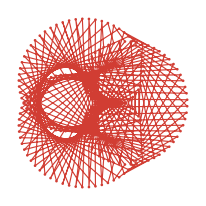
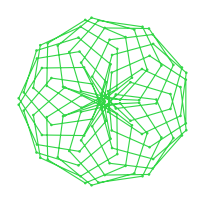
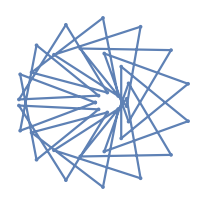

```mathematica
circle=Graphics[Circle[]];
```

```mathematica
Manipulate[
Block[{points, line, p},
p=13;
points = ListPlot[
Table[Labeled[(1+ n * 0.002){Cos[2 π  n / p], Sin[2 π  n/p]}, n], {n,0,x, Sign[x]}],
AspectRatio->1,PlotRange->1.2{{-1,1},{-1,1}} ,Axes->False, GridLines->None
];
line=ParametricPlot[(1+ n * 0.002) {Cos[2 π  n / p], Sin[2 π  n/p]}, {n,0,x +0.00001}];
Show[points, circle,line]
],
{{x,10},-80,80,1}
]
```

```mathematica
style1={{RGBColor[0.8,0.24,0.28], Thickness[0.004]}};
range=1.1{{-1,1},{-1,1}};
```

```mathematica
p=13; k =2;
labels=ListPlot[Table[Labeled[ {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}, n],{n,0,p-1}]];
g= ListPlot[
(
n=#;
m=n*k;
p1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
p2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
{p1, p2}
)&/@Range[p],
 Joined->True, PlotStyle->RGBColor[0.93,0.5,0.5],
 Mesh->All,AspectRatio->1,Axes->False,PlotRange->range
];
Show[g,circle, labels]
```

```mathematica
Manipulate[
Block[{m,path, labels},
labels=ListPlot[Table[Labeled[ {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}, n],{n,0,p-1}]];
path= ListPlot[
(Table[
m=n*k;
{{Cos[m 2 Pi / p], Sin[m 2 Pi / p]} , {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}},
{n,0, p}
]), 
Joined->True,PlotStyle->style1,AspectRatio->1,
Mesh->All, Axes->False,PlotRange->range
];
Show[circle, path, labels]
],
{{p,13},1,300,1},
{{k,3},1,p-1,1}
] (* (37, 13) (43, 14) *)
```

```mathematica
Manipulate[
Block[{m,path},
path= ListPlot[
(Table[
m=n*k;
{Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]},
{n,0, p}
]), 
Joined->True,PlotStyle->style1,AspectRatio->1,
Mesh->All, Axes->False
];
Show[path]
],
{{p,123},1,300,1},
{{k,7},1,p-1,1}
] (* (37, 13) (43, 14) *)
```

```mathematica
Manipulate[
Block[{m,path, border, maxC, range},

border= ListPlot[
Table[
m=n*k;
{Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - t {Cos[n 2 Pi / p], Sin[n 2 Pi / p]},
{n,0, p}
], 
Joined->True,AspectRatio->1,
Mesh->All, Axes->False
];
maxC=Table[{Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - t {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}, {n,0,p}]//Flatten//Max;
range=1.02 maxC{{-1,1},{-1,1}};
path= ListPlot[
(Table[
m=n*k;
{
{Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - t {Cos[n 2 Pi / p], Sin[n 2 Pi / p]},
{Cos[n 2 Pi / p], Sin[n 2 Pi / p]}-t {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}
},
{n,0, p}
]), 
Joined->True,PlotStyle->style1,AspectRatio->1,
Mesh->All, Axes->False, PlotRange->range
];
Show[path, border]
],
{{t,0},0,1},
{{p,123},1,300,1},
{{k,7},1,p-1,1}
] (* (37, 13) (43, 14) *)
```

```mathematica
Accumulate@{a1,a2,a3,a4}
```

```mathematica
{x1,y1}+{x2,y2}
```

```mathematica
{x1,y1}+{x2,y2}+{x3, y3}
```

```mathematica
{a1,a2,a3,a4}//Accumulate
```

```mathematica
Accumulate[{a1,a2,a3,a4}]
```

```mathematica
style2={{RGBColor[0.2,0.24,0.84], Thickness[0.004]}};
```

```mathematica
Manipulate[
Block[{m,path},
path= ListPlot[
Accumulate@(Table[
m=Mod[n*k, p];
 {Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]},
{n,0, p}
]), 
Joined->True,PlotStyle->style2,AspectRatio->1,
Mesh->All
];
Show[path]
],
{{p,23},1,300,1},
{{k,4},1,p,1}
] (* 
(31,16),(44, 23), (x, 23), *)
```

```mathematica
ListConvolve[{1,-1},{a1,a2,a3,a4}]
```

```mathematica
Accumulate[{a1,a2,a3,a4}]
```

```mathematica
ListConvolve[{1,-1},Accumulate@{a1,a2,a3,a4}]
```

```mathematica
UnAccumulate[l_]:=Drop[l,1] - Drop[l,-1]
```

```mathematica
{a2,a3,a4} - {a1,a2,a3}
```

```mathematica
UnAccumulate@{a1,a2,a3,a4}
```

```mathematica
UnAccumulate@Accumulate@{a1,a2,a3,a4}
```

```mathematica
Manipulate[
Block[{m,path},
path= ListPlot[
UnAccumulate@(Table[
m=Mod[n*k, p];
 {Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]},
{n,0, p+1}
]), 
Joined->True,PlotStyle->style2,AspectRatio->1,
Mesh->All
];
Show[path]
],
{{p,23},1,300,1},
{{k,4},1,p-1,1}
] (* {20, 5}, {26, 13}, {30, 6} *)
```

```mathematica
Manipulate[
Block[{m,path},
path= ListPlot[
f@(Table[
m=Mod[n*k, p];
 {Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]},
{n,0, p+1}
]), 
Joined->True,PlotStyle->style2,AspectRatio->1,
Mesh->All
];
Show[path]
],
{f, {Accumulate,Identity, UnAccumulate}},
{{p,23},1,300,1},
{{k,17},1,p,1}
]
```

```mathematica
p=13;
Mod[r^Range[p-1],p]
```

```mathematica
Manipulate[
Block[{n,m,path},
path= ListPlot[
f@((
n=#;
{Cos[ n 2 π/ p], Sin[n 2 π/p]}
)&/@ Mod[r^Range[0,p],p]), 
Joined->True,PlotStyle->style2,AspectRatio->1,Axes->False,
Mesh->All
];
Show[path]
],
{f, {Identity,Accumulate,UnAccumulate}},
{r,{2,3,4,5, 7} },
{{p,211},1,300,1}
]
```

```mathematica
PrimitiveRootList[197]
```

```mathematica
Select[Range[500],MemberQ[PrimitiveRootList[#],5]&]
```

```mathematica
style3={{RGBColor[0.82,0.24,0.20], Thickness[0.004]}};
```

```mathematica
Manipulate[
Block[{n,m,path},
path= ListPlot[
f@((
n=#;
m=n*k;
{Cos[m 2 π/p], Sin[m 2π/ p]} - {Cos[n 2π/p], Sin[n 2 π/p]}
)&/@Mod[r^Range[0,p],p]), 
Joined->True,PlotStyle->style3,AspectRatio->1,Axes->False,
Mesh->All
];
Show[path]
],
{f, {Identity,Accumulate, UnAccumulate}},
{r,{2,3,4,5,6}},
{{p,211},1,1300,1},
{{k,4},1,p-1,1}
]
```

```mathematica
Manipulate[
Block[{n,m,path},
path= ListPlot[
f@((
n=#;
m=Mod[n*k, p];
{Cos[m 2 π/p], Sin[m 2π/p]}-{Cos[n 2π/p], Sin[n 2 π/p]}
)&/@Mod[r^Range[0, p],p]), 
Joined->True,PlotStyle->style3,AspectRatio->1,Axes->False,
Mesh->All
];
Show[path]
],
{f, {Identity,Accumulate, UnAccumulate}},
{r,2,20,1 },
{{p,211},1,300,1},
{{k,4},1,p-1,1}
] (* 
(6, 229, 3), (5, 167, 27|33), (11, 173, 4) 
*)
```

```mathematica
Manipulate[
Grid[Table[
Mod[i^j,p, -(p-1)/2],
{j,1,p-1},
{i,1,p-1}
]
],
{{p,17}, 1,100, 1}
]
```

```mathematica
PrimitiveRootList[173]
```

```mathematica
p=23;Clear[r];Mod[r^Range[p-1],p]
```

```mathematica
p=23;r=11;
Sort[Mod[r^Range[p],p]]//DeleteDuplicates
```

```mathematica
PrimitiveRootList[211]
```

```mathematica
p=173;
Mod[11^Range[p-1], p]
```

```mathematica
DeleteDuplicates[Mod[4^Range[229],229]]//Length
```

```mathematica
EulerPhi[229]
```

```mathematica
DeleteDuplicates[Mod[5^Range[211],212]]//Length
```

```mathematica
Select[Range[1500],MemberQ[PrimitiveRootList[#],4]&]
```

```mathematica
EulerPhi[212]
```

## Legendre Symbol and number of positive points on previous plot

```mathematica
Manipulate[
Block[{m,path},
path= ListPlot[
(Table[
m=Mod[n*k, p];
{Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]},
{n,0, p}
]), 
Joined->True,PlotStyle->style2,AspectRatio->1,
Mesh->All
];
Show[path]
],
{{p,23},1,300,1},
{{k,3},1,p-1,1}
]
```

```mathematica
CountRight[k_, p_]:= Length[Select[
Table[
{Cos[k n 2 Pi / p], Sin[k n 2 Pi / p]} - {Cos[n  2 Pi / p], Sin[n 2 Pi / p]},{n,1, p-1}
], 
#⟦1⟧>-0.00000000001&& #⟦2⟧>-0.00000000001&
]];
```

```mathematica
LegendreSymbol[a_,p_]:=If[MemberQ[ Mod[Range[p-1]^2,p],a],1,-1]
```

```mathematica
LegendreSymbol[4,9]
```

```mathematica
LegendreSymbol[7,9]
```

```mathematica
LegendreSymbol[5,9]
```

```mathematica
l = {22,25,23,29,31,37, 41, 43, 49,53,59,61, 67,91, 1013};
{#,Mod[ CountRight[3, #],3]}&/@l
{#,LegendreSymbol[3,#]}&/@l
```

```mathematica
l =Prime[Range[2,50]];
a={#,If[Mod[CountRight[3, #],3]==0 ,1,-1]}&/@l;
b={#,LegendreSymbol[3,#]}&/@l;
a == b
```

```mathematica
(* takes 1 minute *)
l =Prime[Range[2,500]];
a={#,If[Mod[CountRight[3, #],3]==0 ,1,-1]}&/@l;
b={#,LegendreSymbol[3,#]}&/@l;
a == b
```

```mathematica
l =Range[2,145];
a={#,If[Mod[CountRight[3, #],3]==0 ,1,-1]}&/@l;
b={#,LegendreSymbol[3,#]}&/@l;
a == b
```

```mathematica
{Length[Complement[a,b]],Length[ Complement[b,a]]}
```

```mathematica
Select[Complement[a,b],Mod[#[[1]],3]≠0&]
```

```mathematica
Select[Intersection[a,b],!PrimeQ[#⟦1⟧]&&  Mod[#[[1]],3]≠0&]
```

```mathematica
l = Prime[Range[3,12]];
a={#,If[EvenQ[Mod[CountRight[3, #],3]] ,-1,1]}&/@l
b={#,LegendreSymbol[3,#]}&/@l
a == b
```

## Modular arithmetic, Visualizations of reverse

```mathematica
invPairs={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
facesA={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
facesB={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
circle=Graphics[Circle[]];
```

```mathematica
p=13;
Manipulate[
points = ListPlot[
Table[Labeled[(1+ n * 0.001){Cos[2 π  n / p], Sin[2 π  n/p]}, n], {n,0,x, Sign[x]}],
AspectRatio->1,PlotRange->1.2{{-1,1},{-1,1}} ,Axes->False, GridLines->None
];
line=ParametricPlot[(1+ n * 0.001) {Cos[2 π  n / p], Sin[2 π  n/p]}, {n,0,x +0.00001}];
Show[circle,points, line],
{{x,10},-20,20,1}
]
```

```mathematica
3 / 7 = 6
3 = 6 7
```

```mathematica
a / b = a * (1/b)
```

```mathematica
1/b  * b = 1
```

```mathematica
x * y ==1
```

```mathematica
3 * 1/3
```

```mathematica
2/5 * 5/2
```

```mathematica
Mod[2 * 7, 13]
```

```mathematica
Mod[3 * 9, 13]
```

```mathematica
Mod[5 * 8,  13]
```

```mathematica
p=13;
pairs= Tuples[{Range[p-1],Range[p-1]}]
```

```mathematica
a_List ⊗ b_List := Tuples[{a,b}]
```

```mathematica
{a1,a2,a3}⊗{b1,b2}
```

```mathematica
p=13;
pairs  = Range[p-1]⊗ Range[p-1]
```

```mathematica
invPairs = Select[pairs, Mod[#⟦1⟧ * #⟦2⟧,p]==1&]
```

```mathematica
1 2 3 4 ... 12 = (1  1) ( 2 7 ) (3 9) (5 8) (6 11) 12 

(13 n  + 1) (13 m  + 1)(13 k  + 1)(13 l + 1) == 13 x + 1
12 = (13 - 1)
(13 x + 1) * (13 - 1) = 13 z - 1
```

```mathematica
(13 x + a) * (13 y + b) ≡ a * b  mod 13
```

```mathematica
(p-1)! ≡ -1 ( mod p )
```

```mathematica
style1={{RGBColor[0.2,0.24,0.84], Thickness[0.004]}};
```

```mathematica
points = ListPlot[
Table[Labeled[{Cos[2 π  n / p], Sin[2 π  n/p]}, n], {n,0,p-1}]
];
invLines= ListPlot[
(
{m,n}=#;
{{Cos[2 π  m / p], Sin[2 π  m/p]},{Cos[2 π  n / p], Sin[2 π  n/p]} }
)&/@invPairs,
AspectRatio->1,PlotRange->1.2{{-1,1},{-1,1}} ,PlotStyle->style1,
Axes->False, GridLines->None,Joined->True
];
Show[circle,  points, invLines]
```

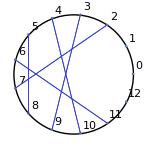

```mathematica
Mod[q * x,  p] == 1 (* x = ? *)
```

```mathematica
p=13; q=3;
Reduce[Mod[q * x, p] == 1,x, Integers]
```

```mathematica
p=33;
(k=#;{k,  Select[Range[p-1], Mod[# * k,p]==1&]})&/@Range[p-1]
```

```mathematica
p=22;
( q=#;{q,  Select[Range[p-1], Mod[# * q,p]==1&]})&/@Range[p-1]
```

Почему обратный элемент единственный? Если
q · m_1 = 1 + n_1· p 
q · m_2 = 1 + n_2 · p
тогда
q · (m_1 – m_2) = (n_1 – n_2) · p 
 то a и b это одна и та же точка на окружности

```mathematica
Reduce[Mod[7 * x,  13] == 1,x, Integers]
```

```mathematica
Reduce[Mod[15 * x,  24] == 1,x, Integers]
```

```mathematica
Reduce[Mod[5 * x,  24] == 1,x, Integers]
```

```mathematica
Reduce[Mod[5* x,  22] == 1,x, Integers]
```

p · m +  q · n  =  1

```mathematica
q * n ≡ 1 (* mod p *)
```

```mathematica
p * m ≡ 1 (* mod q *)
```

```mathematica
p=15; q=7;  r1=p/(2 π); r2=q/(2 π);
plotRange = 1.04{{-r1-2r2, r1+2r2},{-r1-2r2,r1+2r2}};
Manipulate[
Block[{ϕ1,ϕ2,pt, points,allPoints, circle1, circle2},
 ϕ1=l/r1;
 ϕ2=l/r2;
circle1=Circle[{0,0}, r1];
circle2=Circle[(r1+r2){Cos[ϕ1],Sin[ϕ1]}, r2];
pt={PointSize[0.02],RGBColor[0.33,0.36,0.99],Point[(r1+r2){Cos[ϕ1],Sin[ϕ1]} + r2{Cos[π+ϕ2+ϕ1], Sin[π+ϕ2+ϕ1]}]};
allPoints=ListPlot[Table[Labeled[r1{Cos[n 2π/p],Sin[n 2π/p]},n],{n,0,p-1}],PlotStyle->{Gray,PointSize[0.008]}];
points=ListPlot[
Table[r1{Cos[ϕ],Sin[ϕ]},{ϕ,0,ϕ1,(2 π q)/p}],
PlotRange->plotRange,AspectRatio->1,Axes->False,
PlotStyle->{PointSize[0.02],RGBColor[0.3,0.36,0.92]},
PlotLabel->"m = "<>ToString[-Floor[ϕ1/(2 π)]] <>", n = "<>ToString[Floor[ϕ2/(2 π)]]
];
Show[points,allPoints,  Graphics[{circle1,circle2,pt}]]
],
{{l,3}, 0,2 p q,0.1,AnimationRate->1}
]
```

```mathematica
p *  m +  q * n == 1
```

```mathematica
15 *  (-6) +  7 * (13)
```

So, for any pair {p, q}: GCD[p, q] == 1, there exists m : Mod[ m * q, p] == 1.

```mathematica
Manipulate[
Block[{m,path},
path= ListPlot[
Table[
m=Mod[n*q, p];
Labeled[{Cos[m 2 Pi / p], Sin[m 2 Pi / p]},m],
{n,0, p}
], 
Joined->True,PlotStyle->style1,AspectRatio->1,Axes->False,
PlotRange->1.1{{-1,1},{-1,1}},Mesh->All
];
Show[path, circle]
],
{{p,13},1,300,1},
{{ q,3}, 1,p,1}
]
```

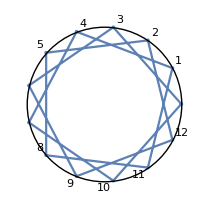

```mathematica
Mod[3 * 9,13]
```

```mathematica
Coprimes[p_]:=Select[Range[p-1],(CoprimeQ[#,p]&)]
```

```mathematica
Coprimes[24]
```

```mathematica
CoprimeQ[24,5]
```

```mathematica
GCD[24,5]==1 (* наибольший общий делитель *)
```

```mathematica
CoprimeQ[24,15]
```

```mathematica
Coprimes[24]
```

```mathematica
{a1,a2,a3}⊗{b1,b2}
```

```mathematica
Times@@@({a1,a2,a3}⊗ {b1,b2})
```

```mathematica
p=24; Coprimes[p] ⊗ Coprimes[p]
```

```mathematica
p=24;
Mod[Times@@@(Coprimes[p] ⊗ Coprimes[p]),p]
```

```mathematica
Tally[{1,3,3,2,3,1,1,1,1}]
```

```mathematica
(*  a * b  *)
p=24;
Tally[Mod[Times@@@(Coprimes[p] ⊗ Coprimes[p]),p]]
```

```mathematica
p=17; l=Coprimes[p]; n = Length[l];
Grid[Table[Mod[l⟦i⟧*l⟦j⟧,p],{i,n},{j,n}]]
```

```mathematica
p=24; l=Coprimes[p]; n = Length[l];
Grid[Table[Mod[l⟦i⟧*l⟦j⟧,p],{i,n},{j,n}]]
```

↑  Multiplicative group of integers modulo p

Coprimes[p] == (ℤ/p ℤ)^×  – multiplicative group of integers modulo p

```mathematica
Length[Coprimes[24]]
Length[Coprimes[24]]==EulerPhi[24] (* Euler's totient function *)
```

```mathematica
p  - 1
```

```mathematica
PowerMod[3, -1, 13]
```

```mathematica
PolynomialMod[1/3, 13]
```

```mathematica
PolynomialMod[1/9, 13]
```

```mathematica
PolynomialMod[1/3, 17]
```

```mathematica
PolynomialMod[1/5, 24]
```

```mathematica
PolynomialMod[1/3, 24]
```

```mathematica
circle=Graphics[Circle[]];
```

```mathematica
Manipulate[
Block[{n,m,pt1,pt2,pairs, labels},
pairs= ListPlot[
(
n=#;
pt1 = {Cos[n 2 π/p], Sin[n 2 π/p]};
m=PolynomialMod[1/n, p]; (* PowerMod[n,-1,p] *)
pt2 = {Cos[m 2 π/p], Sin[m 2 π/p]};
If[pt1≠pt2,{pt1, pt2},{pt1,0.8pt1}]
)&/@Coprimes[p], 
Joined->True,AspectRatio->1,Axes->False,
PlotStyle->{{RGBColor[0.84,0.3,0.28], Thickness[0.002]}},
Mesh->All,PlotRange->1.13{{-1,1},{-1,1}},
PlotLabel->"p="<>ToString[p]
];
labels=ListPlot[Table[Labeled[{Cos[n 2 Pi / p], Sin[n 2 Pi / p]},n ],{n,0,p-1}]];
Show[ pairs,circle]
],
{{p,13},1,300,1}
] 
(* {13, 24, 38, 40, 47, 86, 169, 175, 271} *)
```

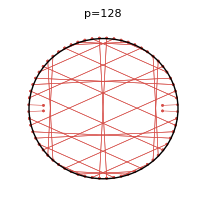
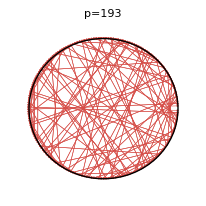
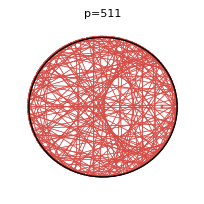

```mathematica
SelfInverses[p_]:=Select[Coprimes[p],Mod[#^2,p]==1&]
```

```mathematica
SelfInverses[24]
```

```mathematica
SelfInverses[32]
```

```mathematica
SelfInverses[18]
```

```mathematica
p->n
```

```mathematica
NormalModulesQ[n_]:=Length[SelfInverses[n]]==2;
```

```mathematica
normals = Select[Range@400, NormalModulesQ]
```

```mathematica
Prime[Range[200]]
```

```mathematica
Select[Prime[Range[200]],(!NormalModulesQ[#])&]
```

```mathematica
5!
```

```mathematica
p=113;
Solve[x^2==1,x,Modulus->p]
```

```mathematica
x^2==1 -> (x-1)(x+1) == 0 (* mod p *)
```

```mathematica
x^2-1 == 0
```

```mathematica
Select[normals, !PrimeQ[#]&]
```

```mathematica
FactorInteger[343]
```

```mathematica
7^3
```

```mathematica
Select[normals, !PrimeQ[#]&& !EvenQ[#]&]
```

```mathematica
xx = Select[normals, !PrimeQ[#]&& EvenQ[#]&]
```

```mathematica
Select[xx/2, !PrimeQ[#]&]
```

Gauss proved, that "normals"  are { 1,2,4,p^k,2 p^k}, p is odd prime.
For these n  ∈ { 1,2,4,p^k,2 p^k} group (ℤ/n ℤ)^× is cyclic.

```mathematica
x, x x, x x x,
```

```mathematica
Select[Range@200,Length[SelfInverses[#]]==4&]
```

```mathematica
Select[Range@200,Length[SelfInverses[#]]==6&]
```

```mathematica
Select[Range@200,Length[SelfInverses[#]]==8&]
```

```mathematica
crazy2 = Select[Range@400,Length[SelfInverses[#]]==4&]
```

```mathematica
FactorInteger[20]
```

```mathematica
FactorInteger[20]
```

```mathematica
Times@@(Power@@@FactorInteger[20])
```

```mathematica
Times@@(Power@@@{{a,x},{b,y},{c,z}})
```

```mathematica
Times@@(Power@@@{{2,1},{3,2},{5,1}})
```

```mathematica
Wedge@@(Subscript@@@FactorInteger[45])
```

```mathematica
FactorIntegerExpr[n_]:=Wedge@@(Subscript@@@FactorInteger[n]);
SetAttributes[FactorIntegerExpr, Listable];
```

```mathematica
crazy2
```

```mathematica
FactorIntegerExpr[crazy2]
```

```mathematica
ClearAll[Wedge];
```

```mathematica
Wedge[Subscript[2, _],y__]:=Wedge[y];
Wedge[Subscript[2, _]]:=1;
Wedge[x_]:=x;
```

```mathematica
FactorIntegerExpr[crazy2]
```

```mathematica
Length[{1,2,3,4,5}]
```

```mathematica
{1,2,3,4,5}
```

```mathematica
List[1,2,3,4,5]
```

```mathematica
Length[ff[3,4,5,6]]
```

```mathematica
Length/@FactorIntegerExpr[crazy2]
```

## Visialization of inverse by summation of vec(a, 1 / a)

```mathematica
style1={{RGBColor[0.22,0.24,0.80], Thickness[0.008]}};
style2={{RGBColor[0.42,0.40,0.20], Thickness[0.008]}};
style3={{RGBColor[0.82,0.24,0.20], Thickness[0.008]}};
style4={{RGBColor[0.24,0.84,0.22], Thickness[0.008]}};
```

```mathematica
Coprimes[p_]:=Select[Range[p-1],(CoprimeQ[#,p]&)]
```

```mathematica
Coprimes[24]
```

```mathematica
circle=Graphics[Circle[]];
```

```mathematica
Manipulate[
Block[{n,m,pt1,pt2,path},
labels=ListPlot[Table[ Labeled[{Cos[m 2 π/p], Sin[m 2 π / p]},m],{m, 0, p-1 }]];
path= ListPlot[
((
n=#;
pt1 = {Cos[n 2 π/p], Sin[n 2 π/p]};
m=PolynomialMod[1/n,p]; (* PowerMod[n,-1,p] *)
pt2 = {Cos[m 2 π/p], Sin[m 2 π / p]};
{pt1,pt2}
)&/@Coprimes[p]), 
Joined->True,AspectRatio->1,Axes->False,PlotStyle->style1,Mesh->All,
PlotLabel->"p="<>ToString[p]
];
Show[circle, path, labels]
],
{{p,13},1,300,1}
]  (* 
{17, 23, 32, 37, 71, 83, 88, 140} *)
```

```mathematica
Manipulate[
Block[{n,m,pt1,pt2,path},
path= ListPlot[
(
n=#;
pt1 = {Cos[n 2 π/p-Pi/2], Sin[n 2 π/p - Pi/2]};
m=PolynomialMod[1/n,p]; (* PowerMod[n,-1,p] *)
pt2 = {Cos[m 2 π/p -Pi/2], Sin[m 2 π / p - Pi/2]};
{pt1, pt2 + pt1}
)&/@Coprimes[p], 
Joined->True,AspectRatio->1,Axes->False,
PlotStyle->style2,Mesh->All,
PlotLabel->"p="<>ToString[p]
];
Show[circle,  path]
],
{{p,71},1,300,1}
]
```

```mathematica
{x1,y1} - {x2, y2}
```

```mathematica
Manipulate[
Block[{n,m,pt1,pt2,path},
path= ListPlot[
((
n=#;
pt1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
m=PolynomialMod[1/n, p]; (* PowerMod[n, -1, p] *)
pt2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
pt2- pt1
)&/@Coprimes[p]), 
Joined->True,AspectRatio->Automatic,Axes->False,
PlotStyle->style3,Mesh->All,
PlotLabel->"p="<>ToString[p]
];
Show[ path]
],
{{p,13},1,300,1}
]
```

```mathematica
Accumulate[{a1,a2,a3,a4}]
```

```mathematica
Accumulate[{{x1,y1} , {x2, y2},{x3,y3}}]
```

```mathematica
Manipulate[
Block[{n,m,pt1,pt2,path},
path= ListPlot[
Accumulate@((
n=#;
pt1 = {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
m=PolynomialMod[1/n, p]; (* PowerMod[n, -1, p] *)
pt2 = {Cos[m 2 Pi / p], Sin[m 2 Pi / p]};
pt2- pt1
)&/@Coprimes[p]), 
Joined->True,AspectRatio->1,Axes->False,
PlotStyle->style3,Mesh->All,
PlotLabel->"p="<>ToString[p]
];
Show[ path]
],
{{p,13},1,300,1}
]
```

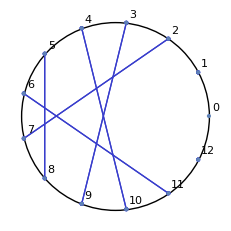
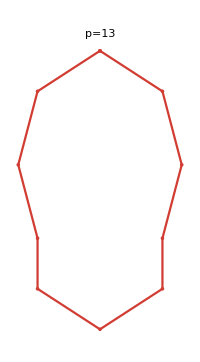

```mathematica
UnAccumulate[l_]:=Drop[l,1] - Drop[l,-1]
```

```mathematica
UnAccumulate[{a1,a2,a3,a4}]
```

```mathematica
UnAccumulate[{a1,a1 + a2,a1 + a2+ a3, a1 + a2+a3 + a4}]
```

```mathematica
Manipulate[
Block[{n,m,pt1,pt2,path},
path= ListPlot[
UnAccumulate@((
n=#;
pt1 = {Cos[n 2 π/p], Sin[n 2 π/p]};
m=PolynomialMod[1/n,p]; (* PowerMod[n,-1,p] *)
pt2 = {Cos[m 2 π/p], Sin[m 2 π / p]};
pt1- pt2
)&/@Coprimes[p]), 
Joined->True,AspectRatio->1,Axes->False,
PlotStyle->style4,Mesh->All,
PlotLabel->"p="<>ToString[p]
];
Show[path]
],
{{p,17},1,300,1}
]
```

## NumberFaces

```mathematica
style={{RGBColor[0.2,0.84,0.28], Thickness[0.002]}};
```

```mathematica
NumberInvPairs[p_]:=Module[{m,n, pt1, pt2},
ListPlot[
((
n=#;
m=PolynomialMod[1/n, p];
pt1={Cos[m 2 Pi / p], Sin[m 2 Pi / p]} ;
pt2= {Cos[n 2 Pi / p], Sin[n 2 Pi / p]};
If[pt1≠pt2,{pt1, pt2},{pt1,0.8pt1}]
)&/@Coprimes[p]
), 
Joined->True,Axes->False,AspectRatio->1,Mesh->All, Epilog->Text["p="<>ToString[p],{Center,Center}],
PlotStyle->{ColorData[Mod[p,60]+1][Mod[p,7]]}
]
]
```

```mathematica
NumberFaceA[p_]:=Module[{m,n},
ListPlot[
Accumulate@((
n=#;
m=PolynomialMod[1/n, p];{Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}
)&/@Coprimes[p]
), 
Joined->True,Axes->False,AspectRatio->1,Mesh->All, Epilog->Text["p="<>ToString[p],{Center,Center}],
PlotStyle->{ColorData[Mod[p,60]+1][Mod[p,7]]}
]
]
```

```mathematica
NumberFace[p_]:=Module[{m,n},
ListPlot[
((
n=#;
m=PolynomialMod[1/n, p];
 {Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}
)&/@Coprimes[p]
), 
Joined->True,Axes->False,AspectRatio->1,Mesh->All,
PlotRange->All, Epilog->Text["p="<>ToString[p],{Center,Center}],
PlotStyle->{ColorData[Mod[p,60]+1][Mod[p,7]]}
]
];
NumberFaceB[p_]:=Module[{m,n, pt1,pt2,path},
path=ListPlot[
((
n=#;
m=PolynomialMod[1/n, p];
pt1={Sin[m 2 Pi / p], -Cos[m 2 Pi / p]} ;
pt2={Sin[n 2 Pi / p], -Cos[n 2 Pi / p]};
{pt1,pt1+pt2}
)&/@Coprimes[p]
), 
Joined->True,Axes->False,AspectRatio->Automatic,Mesh->All, Epilog->Text["p="<>ToString[p],{Center,Center}],
PlotStyle->{ColorData[Mod[p,60]+1][Mod[p,7]]}
];
Show[path, Graphics[Circle[]]]
];
NumberFacesX[n_]:={NumberFaceA[n], NumberFace[n],NumberFaceB[n] }
```

```mathematica
SetOptions[{Plot, ListPlot}, GridLines->None];
```

```mathematica
NumberFacesX[#]&/@Range[20]
```

```mathematica
NumberFacesX[#]&/@{47}
```

```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
NumberFacesX[#]&/@{9, 18}
```

```mathematica
NumberFacesX[#]&/@{25, 50, 100}
```

```mathematica
NumberFacesX[#]&/@{42}
```

```mathematica
NumberFacesX[#]&/@{2,4,8,16,32, 64}
```

```mathematica
NumberFacesX[#]&/@{3, 9, 27, 81}
```

```mathematica
NumberFacesX[#]&/@{5, 25, 125}
```

```mathematica
NumberFacesX[#]&/@{41,69,70}
```

```mathematica
NumberFaceLabeled[p_]:=Module[{m,n},
ListPlot[
Labeled[#⟦1⟧,#⟦2⟧]&/@Transpose[{
Accumulate@((
n=#;
m=PolynomialMod[1/n, p];
 {Cos[m 2 Pi / p], Sin[m 2 Pi / p]} - {Cos[n 2 Pi / p], Sin[n 2 Pi / p]}
)&/@Coprimes[p]
),
Coprimes[p]
}], 
Joined->True,Axes->False,AspectRatio->1,Mesh->All, Epilog->Text["p="<>ToString[p],{Center,Center}],
PlotStyle->{ColorData[Mod[p,60]+1][Mod[p,7]]}
]
]
```

```mathematica
NumberFaceLabeled[41]
```

```mathematica
NumberFaceA[#]&/@Select[Range[20],Length[Coprimes[#]]>2&]
```

```mathematica
facesA=NumberFaceA[#]&/@Select[Range[50, 61],Length[Coprimes[#]]>4&]
```

```mathematica
facesA=NumberFaceA[#]&/@Select[Range[50, 61],Length[Coprimes[#]]>4&]
```

```mathematica
faces=NumberFace[#]&/@Select[Range[50, 61],Length[Coprimes[#]]>4&]
```

```mathematica
facesB=NumberFaceB[#]&/@Select[Range[40, 61],Length[Coprimes[#]]>4&]
```

```mathematica
facesA={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
facesA100=NumberFace[#]&/@Select[Range[100],Length[Coprimes[#]]>4&]
```

```mathematica
facesA100={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
{
-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,
-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-
}
```

```mathematica
NumberFacesX[66]
```

```mathematica
NumberFacesX[255]
```

```mathematica
NumberFacesX[256]
```

```mathematica
(0.5438 - 0.5964)/ (0.2733 - 0.1677)
```

```mathematica
NumberFacesX[169]
```

```mathematica
NumberFacesX[243]
```

```mathematica
NumberFacesX[5^4]
```

```mathematica
NumberFacesX[5^4+1]
```

## NumberFaceB

```mathematica
SetAttributes[NumberFaceB,Listable];
```

```mathematica
NumberFaceB[Prime[Range[1,20]]]
```

```mathematica
{NumberFaceB[Prime[Range[1,20]]],NumberFaceB[2 Prime[Range[1,20]]]}//Transpose
```

## Signatures and Legendre symbol (Jacoby simbol)

```mathematica
(p | q) * (q | p) = (-1)^((p-1)/2(q-1)/2)
```

```mathematica
p=19;
sigs={#[[1]],Signature[#]}&/@Table[
Mod[i*j,p],
{i,1,  p-1},
{j,1,  p-1}
]
```

```mathematica
Table[{i, Mod[i^((p-1)/2) ,p]},{i,1,p-1}]
```

```mathematica
Mod2[a_,p_]:=Mod[a + (p-1)/2,p]-(p-1)/2;
p=19;
pows=Table[{i, Mod2[i^((p-1)/2) ,p]},{i,1,p-1}]
```

```mathematica
jacobies={#,JacobiSymbol[#,19]}&/@Range[1,18]
```

```mathematica
sigs==pows
```

```mathematica
sigs==jacobies
```

```mathematica
?? JacobiSymbol
```

```mathematica
Grid[Table[
Mod[i*j,p],
{i,1,  p-1},
{j,1,  p-1}
]]
```

```mathematica
Grid[Table[
If[i==j,Style[Mod[i*j,p],Bold],Mod[i*j,p]],
{i,1,  p-1},
{j,1,  p-1}
]]
```

```mathematica
{JacobiSymbol[1,19],JacobiSymbol[4,19], JacobiSymbol[9,19], JacobiSymbol[16,19], JacobiSymbol[11,19],  JacobiSymbol[7,19], JacobiSymbol[5,19], JacobiSymbol[17,19]}
```

```mathematica
{JacobiSymbol[2,19],JacobiSymbol[3,19], JacobiSymbol[8,19], JacobiSymbol[10,19],  JacobiSymbol[12,19], JacobiSymbol[13,19],JacobiSymbol[14,19], JacobiSymbol[15,19] }
```

```mathematica
(* For prime number p: *)
LegendreSymbol[m_, p_]:=  "1 if exists a: Mod[a^2, p] == m, -1 otherwise"
```

```mathematica
Clear[m]
```

```mathematica
Thread[PowerMod[Range[p-1], 2, p]==m]
```

```mathematica
If[Or@@Thread[PowerMod[Range[p-1], 2, p]==m],1,-1]
```

```mathematica
LegendreSymbol[m_, p_]:=If[Or@@Thread[PowerMod[Range[p-1],2,p]==m],1,-1];
```

```mathematica
LegendreSymbol[#, p]&/@Range[p-1]
```

```mathematica
PowP2[m_, p_]:= Mod2[ m^((p - 1) / 2) , p];
SignP[m_, p_]:=Signature[Table[Mod[m * i,p], {i, 1, p-1}]]
```

```mathematica
PowP2[#,p]&/@Range[p-1]
```

```mathematica
SignP[#,p]&/@Range[p-1]
```

```mathematica
(* if m = a^2*)
Mod2[ m^((p - 1) / 2) , p] == Mod2[ a^(p - 1) , p] == 1;
```

```mathematica
Mod2[1 a * 2 a * 3 a * 4 a ... (p-1) a, p ]== Mod[1 * 2  * 3  * 4  ... (p-1), p]
Mod[a^(p-1), p] == 1
```

```mathematica
x ==  m^((p - 1) / 2) ;
x^2 == m^(p - 1)= 1;
x == 1 | -1;
```

```mathematica
x^2-1 ==  (x-1) (x+1)
```

```mathematica
Mod[a^2,p]==m;
x^2-m == (x-a) (x+a)
```